Prelim work on how to decompose an unitary matrix into the CKM parameter forms.

```mathematica
Clear["Global`*"]
```

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/Peggy/Projects/physics_5d_flavourful_axion_neutrino/mathematica

```mathematica
<<"WarpFlavourAxion`"
```

FermionProfile::shdw: Symbol FermionProfile appears in multiple contexts {WarpFlavourAxion`,Global`}; definitions in context WarpFlavourAxion` may shadow or be shadowed by other definitions.

### Functions

#### CKM matrix

```mathematica
Ckm[t12_,t13_,t23_,delta_]:=({{1, 0, 0}, {0, Cos[t23], Sin[t23]}, {0, -Sin[t23], Cos[t23]}}).({{Cos[t13], 0, Sin[t13]Exp[-I delta]}, {0, 1, 0}, {-Sin[t13]Exp[I delta], 0, Cos[t13]}}).({{Cos[t12], Sin[t12], 0}, {-Sin[t12], Cos[t12], 0}, {0, 0, 1}})
```

Check the real value

```mathematica
Map[Abs,Ckm[13.04 Degree, 0.201 Degree, 2.38 Degree, 1.20],{-1}]//MatrixForm
```

(0.974207 | 0.22563 | 0.0035081
0.225488 | 0.973361 | 0.0415266
0.00873301 | 0.0407493 | 0.999131)

The actual value is

(0.97427±0.00015 | 0.22534±0.00065 | 0.00351±0.00015
0.22520±0.00065 | 0.97344±0.00016 | 0.0412±0.0011
0.00867±0.00031 | 0.0404±0.0011 | 0.999146±0.000046)

```mathematica
GetCKMthetas[unitaryMatrix_]:=Module[{abss,args,c12,c13,c23},
(* unitaryMatrix must be 3 by 3 matrix *)
abss=Map[Abs,unitaryMatrix,{-1}];
args=Map[Arg,unitaryMatrix,{-1}];
c13 = Sqrt[1-abss[[1, 3]]^2];
c12 = abss[[1, 1]]/c13;
c23 = abss[[3, 3]]/c13;
(* output theta angles *)
{ArcCos[c12],ArcCos[c13],ArcCos[c23]}
]
```

```mathematica
GetCKMParameters[unitaryMatrix_]:=Module[{abss,args,c12,c13,c23,s12,s13,s23,delta,u1},
(* unitaryMatrix must be 3 by 3 matrix *)
abss=Map[Abs,unitaryMatrix,{-1}];
args=Map[Arg,unitaryMatrix,{-1}];

(* CKM parameters *)
s13=abss[[1, 3]];c13 = Sqrt[1-s13^2];
c12 = abss[[1, 1]]/c13;s12=Sqrt[1-c12^2];
c23 = abss[[3, 3]]/c13;s23=Sqrt[1-c23^2];

(* solving for rotation parameters *)
u1=1/2 Arg[-
Exp[-I/3(4 args[[1,1]]+args[[1,2]]+2 args[[2, 3]]+2 args[[3, 3]])] (Exp[I( args[[2, 1]]+ args[[3, 3]])]c23 abss[[2,1]] -Exp[I(args[[2, 3]]+args[[3, 1]])]s23 abss[[3,1]])
];
(* solving for the CP phase *)
delta=Mod[2Pi-1/3(6u1+args[[1,1]]+args[[1,2]]+3args[[1,3]]-args[[2 ,3]]-args[[3,3]]),2Pi];

(* output {CKM parameter, phi_u, phi_d} *)
{
{ArcCos[c12],ArcCos[c13],ArcCos[c23],delta},
{u1,
-u1+1/3 (-args[[1,1]]-args[[1,2]]-2 args[[2,3]]+args[[3,3]]),
-u1+1/3 (-args[[1,1]]-args[[1,2]]+args[[2,3]]-2 args[[3,3]])},
{u1+args[[1,1]],
u1+args[[1,2]],
-u1+1/3 (-args[[1,1]]-args[[1,2]]+args[[2,3]]+args[[3,3]])}
}
]
```

### Workspace

```mathematica
m = RandomUnitaryMatrix[3, 0.1, 4];
m//MatrixForm
```

(-0.453915-0.491285 ⅈ | 0.135348+0.726795 ⅈ | 0.00816704-0.077345 ⅈ
0.321109+0.622186 ⅈ | -0.021538+0.639122 ⅈ | 0.274047+0.16041 ⅈ
0.23345-0.0887376 ⅈ | 0.167623+0.128106 ⅈ | -0.717611+0.614941 ⅈ)

```mathematica
(* m= {
{(-0.6172793291062022-0.12243613860981267I),(0.5084885671803796-0.489200419247175I), (0.2727797775870358-0.17801444215376286I)},
{(-0.04928590865099306-0.5355437544935865I), (-0.29260820623132106+0.10273110586065624I), (-0.12706133045873297-0.7735928916866746I)},
{(-0.09426843489504314-0.5530396642505069I), (-0.4439850292872076-0.4569752489564456I), (-0.11713696213209661+0.5153546736574932I)}
}
*)
```

```mathematica
{ckms,phiu, phid} =GetCKMParameters[m]
```

{{0.835358,0.0778537,0.324154,1.74908},{0.507031,0.260954,-1.64257},{-1.80965,1.89371,0.790522}}

These two matrices should be exactly the same

```mathematica
Ckm@@ckms  //Chop// MatrixForm
DiagonalMatrix[Exp[I phiu]].m.DiagonalMatrix[Exp[-I phid]]// Chop// MatrixForm
```

(0.66888 | 0.739291 | -0.013793-0.0765422 ⅈ
-0.69997-0.0163563 ⅈ | 0.639229-0.0180781 ⅈ | 0.317542
0.244957-0.0486787 ⅈ | -0.203995-0.0538029 ⅈ | 0.945049)

(0.66888 | 0.739291 | -0.013793-0.0765422 ⅈ
-0.69997-0.0163563 ⅈ | 0.639229-0.0180781 ⅈ | 0.317542
0.244957-0.0486787 ⅈ | -0.203995-0.0538029 ⅈ | 0.945049)

These two matrices should be exactly the same

```mathematica
Map[Abs,Ckm@@ckms ,{-1}] //Chop// MatrixForm
Map[Abs,DiagonalMatrix[Exp[I phiu]].m.DiagonalMatrix[Exp[-I phid]],{-1}]// Chop// MatrixForm
```

(0.66888 | 0.739291 | 0.077775
0.700162 | 0.639485 | 0.317542
0.249746 | 0.210971 | 0.945049)

(0.66888 | 0.739291 | 0.077775
0.700162 | 0.639485 | 0.317542
0.249746 | 0.210971 | 0.945049)

```mathematica
(* 
{u1,m1,v1}=SingularValueDecomposition[y1tilde];
{u2,m2,v2}=SingularValueDecomposition[y2tilde];
mat = y1.ConjugateTranspose[v2]; ckmsTemp = GetCKMParameters[mat][[1]];
Abs[((ckmsTemp[[1]]-$CkmTheta12)/($CkmTheta12Sigma))^2+((ckmsTemp[[2]]-$CkmTheta13)/($CkmTheta13Sigma))^2+((ckmsTemp[[3]]-$CkmTheta23)/($CkmTheta23Sigma))^2+((ckmsTemp[[4]]-$CkmDelta)/($CkmDeltaSigma))^2]
*)
```

```mathematica
SquaredError[y1_,y2_,cL1_,cL2_,cL3_,mcR11_,mcR12_,mcR13_,mcR21_,mcR22_,mcR23_,zuv_:1.01,zir_:10]:=Module[{y1tilde,y2tilde,u1,m1,v1,u2,m2,v2,mat,ckmsTemp},
(*  *)
y1tilde=DiagonalMatrix[{FermionProfile[cL1,zuv,zir,zuv] ,FermionProfile[cL2,zuv,zir,zuv] ,FermionProfile[cL3,zuv,zir,zuv]}].y1.DiagonalMatrix[{FermionProfile[mcR11,zuv,zir,zuv] ,FermionProfile[mcR12,zuv,zir,zuv] ,FermionProfile[mcR13,zuv,zir,zuv]}];
y2tilde=DiagonalMatrix[{FermionProfile[cL1,zuv,zir,zuv] ,FermionProfile[cL2,zuv,zir,zuv] ,FermionProfile[cL3,zuv,zir,zuv]}].y2.DiagonalMatrix[{FermionProfile[mcR21,zuv,zir,zuv] ,FermionProfile[mcR22,zuv,zir,zuv] ,FermionProfile[mcR23,zuv,zir,zuv]}];
{u1,m1,v1}=SingularValueDecomposition[y1tilde];
{u2,m2,v2}=SingularValueDecomposition[y2tilde];
mat = u1.ConjugateTranspose[u2]; ckmsTemp = GetCKMParameters[mat][[1]];
Abs[((ckmsTemp[[1]]-$CkmTheta12)/($CkmTheta12Sigma))^2+((ckmsTemp[[2]]-$CkmTheta13)/($CkmTheta13Sigma))^2+((ckmsTemp[[3]]-$CkmTheta23)/($CkmTheta23Sigma))^2+((ckmsTemp[[4]]-$CkmDelta)/($CkmDeltaSigma))^2]
]
```

```mathematica
y1temp = RandomMatrix[3];y2temp=RandomMatrix[3];
SquaredError[y1temp, y2temp, 3., 2., 1., 1.3, 1.2, 1.1, 1.3, 1.2, 1.1]
```

7.11578×10^7

```mathematica
NMinimize[SquaredError[y1temp,y2temp,c1,c2,c3,d11,d12,d13,d21,d22,d23],
{c1,c2,c3,d11,d12,d13,d21,d22,d23}
]
```

SingularValueDecomposition::svdnsvc: Cannot compute all the singular vectors.

Set::shape: Lists {u2$6324,m2$6324,v2$6324} and SingularValueDecomposition[{«1»}] are not the same shape.

Function::slot: Slot[Abs[1]] (in Abs[-3.65654×10^-19-9.29195×10^-20 ⅈ] Conjugate[FermionProfile[Abs[c1],Abs[1.01],Abs[10],Abs[1.01]]]^Abs[3] «5» FermionProfile[Abs[d12],Abs[1.01],Abs[10],Abs[1.01]] FermionProfile[Abs[d13],Abs[1.01],Abs[10],Abs[1.01]]+«1»+«10»+Abs[1.] Slot[«1»]^Abs[3]&) should contain a non-negative integer or string.

General::stop: Further output of Function::slot will be suppressed during this calculation.

Root::npoly: (Abs[-3.65654×10^-19-9.29195×10^-20 ⅈ] Conjugate[FermionProfile[Abs[c1],Abs[1.01],Abs[10],Abs[1.01]]]^Abs[3] «5» FermionProfile[Abs[d12],Abs[1.01],Abs[10],Abs[1.01]] FermionProfile[Abs[d13],Abs[1.01],Abs[10],Abs[1.01]]+«11»+Abs[1.] («1»)^(«1»)&)[#1] is not a polynomial in #1.

General::stop: Further output of Root::npoly will be suppressed during this calculation.

Root::rnum: 0 is not a valid root number.

General::stop: Further output of Root::rnum will be suppressed during this calculation.

Part::partw: Part 3 of {{Power[<<2>>] <<1>>, <<2>>}, <<2>>} . Co<<15>>e[<<1>>] does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

$Aborted

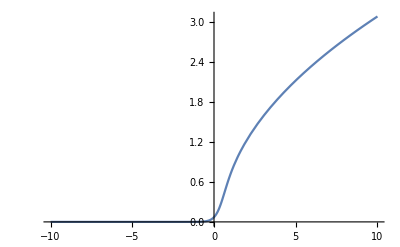

```mathematica
Plot[FermionProfile[c,1.,100.,1.],{c,-10,10}]
```

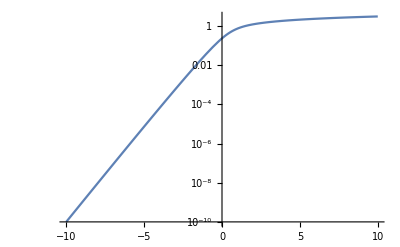

```mathematica
LogPlot[FermionProfile[c,1.,10.,1.],{c,-10,10}]
```

```mathematica
FermionProfile[0., 1.01, 10.]
```

0.240574